# 知識構造化法

Update: 20131021

2013年度　秋学期、筑波大学　学部3・4年次、5・6限

## 1.知識構造化とは

[講義室]

### 知識構造化法ガイダンス

「知識」も「構造」も明確な定義はなく、「知識構造化」もなんだかよくわからない。

ここでは、そのような問題には分け入らず、「探索的データ解析」を中心に学ぶ。 -> [4.探索的データ解析]

ある程度の理論の解説もありますが、Mathematica等を利用して実践的な解析ができる技術を身につけるための授業です。Linux上でC言語も使用します。
なんらかのプログラミング経験があることが望ましいですが、初心者に対しても丁寧に指導します。
初回は自己紹介的なことをやってもらいます。授業方針に対するリクエストは歓迎です。

履修者確認

希望調査等

プログラミング言語の経験 -> Ruby

出席 -> とらない

期末試験 -> 行なわない

レポートあり

授業中の回答で加点

### 知識構造化とは

スライド: 知識構造化法_中山先生/知識構造化法1.pptx

表現の変換・解釈 
図やチャートを用いて情報や思考を分かりやすく示す

構造の付加(メタデータの付与)
スライド:知識構造化法_中山先生/知識構造化法1-2.pptx

尺度水準
スライド:知識構造化法_中山先生/知識構造化法1-2.pptx

[実習室]

腕試し 
フィボナッチ数列の第n項を求める関数のプログラム(再帰)

R

Mathematica

2013/10/03

## 2.データの構造について

Mathematicaにおけるデータ構造とデータの構造化

Mathematicaの言語構造は、一貫してリスト型である。リスト構造であれば直接扱うことができる。リストより高次の構造は、予約済み関数がサポートする。

データ構造の前にデータ処理とは何かについて学ぶ。

Mathematicaによるフィボナッチ数列のプログラムは後ほど。

### データとは

処理系が扱える表現全てがデータである。

ちなみに: 演算装置内の処理を考えるとき、「instruction」と「data」に分けて考える。ここでの「data」は別の概念と捉えたほうがよいであろう。

### データ処理とは

スライド: turing.odp

データ処理とは、処理対象と処理命令の定義が記述された表現を、その表現以外の知識(ルール)を用い、表現が変化しなくなるまで評価を続けることである(べつの言葉で言えば、表現評価系を用いた表現の変換)。処理対象と処理命令は、分離が曖昧であり広い意味ではすべて処理対象である。

「計算機」と「データ」を抽象化するとチューリングマシンの概念となる。「人間からの割り込みを許すチューリングマシン」の実装が「計算機」である。

#### チューリングマシン

スライド: turing.odp

```mathematica
??TuringMachine
```

RowBox[{"TuringMachine", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", StyleBox["t", "TI"]}], "]"}] 指定されたルールで初期条件 StyleBox["init", "TI"] から StyleBox["t", "TI"] ステップ進んだチューリングマシンの進化を表すリストを生成する． 
RowBox[{"TuringMachine", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"]}], "]"}] StyleBox["init", "TI"] を1ステップ進化させた結果を与える．

Attributes[TuringMachine]={Protected,ReadProtected}

```mathematica
??IntegerDigits
```

RowBox[{"IntegerDigits", "[", StyleBox["n", "TI"], "]"}] 十進数表記における整数 StyleBox["n", "TI"] の桁数字をリスト形式で返す．
RowBox[{"IntegerDigits", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["b", "TI"]}], "]"}] StyleBox["b", "TI"] 進数における桁数字を整数 StyleBox["n", "TI"] のリストで返す．
RowBox[{"IntegerDigits", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["b", "TI"], ",", StyleBox["len", "TI"]}], "]"}] この書式を使うと，リスト長が StyleBox["len", "TI"] になるよう出力されるリストの左側にゼロが付け足される．

Attributes[IntegerDigits]={Listable,Protected}

```mathematica
IntegerDigits[2506,2]
```

{1,0,0,1,1,1,0,0,1,0,1,0}

```mathematica
??FromDigits
```

RowBox[{"FromDigits", "[", StyleBox["list", "TI"], "]"}] 十進法の桁数字からなるリストから単一整数を構築する．
RowBox[{"FromDigits", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["b", "TI"]}], "]"}] StyleBox["b", "TI"] を底とする桁数字を使う．
RowBox[{"FromDigits", "[", StyleBox["\"\!\(\*StyleBox[\"string\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] 桁数字の列から単一整数を構築する．
RowBox[{"FromDigits", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"string\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["\"Roman\"",ShowStringCharacters->True]}], "]"}] ローマ数字から整数を構築する．

Attributes[FromDigits]={Protected}

```mathematica
FromDigits[{1,0,0,1,1,1,0,0,1,0,1,0},2]
```

2506

```mathematica
turingCurrentState[s_,k_]:=Module[
{sets,setk,current},
sets=Range[0,s-1];
setk=Range[0,k-1];
current=Flatten[Outer[List,sets,setk],1]
]
```

```mathematica
turingAllRules[s_,k_]:=Module[
{(*numrule,*)numStateSet,numOperateSet,sets,setk,(*current,*)selections,next},
(*numrule=(2 s k)^(s k);*)
numStateSet=s k;
numOperateSet=2 s k;
sets=Range[0,s-1];
setk=Range[0,k-1];
selections=Tuples[Range[numOperateSet],numStateSet];
next=Flatten[Outer[List,sets,setk,{"L","R"}],2];
Map[next[[#]]&,selections]
]
```

#### セルオートマトン

```mathematica
??CellularAutomaton
```

RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", StyleBox["t", "TI"]}], "]"}] 指定した条件でセルオートマトンを初期条件 StyleBox["init", "TI"] から StyleBox["t", "TI"] ステップ実行した進化を表すリストを生成する．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"]}], "]"}] 1ステップ分の StyleBox["init", "TI"] の進化の結果を返す．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["tspec", "TI"], ",", StyleBox["xspec", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["tspec", "TI"]，StyleBox[RowBox[{"xspec", " "}], "TI"]等で指定された進化の部分だけを返す．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["t", "TI"], ",", "All", ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["t", "TI"] ステップの間に影響を受けるであろうすべてのセルを各ステップに含む．

Attributes[CellularAutomaton]={Protected}

```mathematica
FromDigits[{0,0,0,1,0,0,0,1},2]
```

17

```mathematica
numRuleToCellList[n_,d_]:=(* n: 第nルール、d: d次元 *)
Module[{dig,stats,box,bbox,cellstat},
dig=3^d;
stats=2^dig;
bbox=Reverse[Map[IntegerDigits[#,2,dig]&,Range[0,stats-1]]];
cellstat=IntegerDigits[n,2,stats];
Transpose[{bbox,cellstat}]
]
```

```mathematica
cellListVis1D[rule_]:=Grid[{Map[Grid[{#[[1]],{Null,#[[2]],Null}},Frame->All]&,rule]}]
```

1近傍、1次元、第0ルール

```mathematica
cellListVis1D[numRuleToCellList[2,1]]
```

1 | 1 | 1
 | 0 |  | 1 | 1 | 0
 | 0 |  | 1 | 0 | 1
 | 0 |  | 1 | 0 | 0
 | 0 |  | 0 | 1 | 1
 | 0 |  | 0 | 1 | 0
 | 0 |  | 0 | 0 | 1
 | 1 |  | 0 | 0 | 0
 | 0 |

### プログラミング言語とは

効率的にデータ処理を行うためにコンパイラ(インタープリタ)が対応すべき表現 :

抽象化(変数)
 ポインタもアドレスを格納する変数に過ぎない。

繰り返し(または再帰)
    再帰表現と繰り返し表現は可換であるが、書き直しの手間がかかるため、双方備えるべき。

条件分岐

### データ型

Mathematicaの場合、Headによって返されるオブジェクトと理解すればよい。自動的に付与される。

```mathematica
Head[a]
```

Symbol

```mathematica
Head[6]
```

Integer

```mathematica
Head[6.]
```

Real

```mathematica
Symbol["t"]
```

t

```mathematica
Head[fib]
```

Symbol

#### リスト

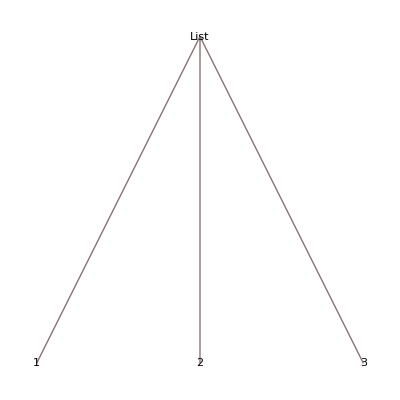

```mathematica
TreeForm[{1,2,3}]
```

#### ツリー

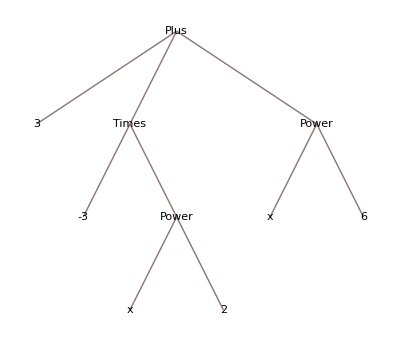

```mathematica
TreeForm[x^6-3x^2+3]
```

```mathematica
TreeForm[7^6-7*8+2]
```

-Graphics-

#### グラフ

リストでグラフは直接表現できないので、 Graph[]という予約済み関数を使う。

```mathematica
??Graph
```

RowBox[{"Graph", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] 辺 SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]]のグラフを与える．
RowBox[{"Graph", "[", RowBox[{RowBox[{StyleBox["{", "TI"], RowBox[{StyleBox[SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], "TI"], ",", StyleBox[SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], "TI"], ",", StyleBox["…", "TR"]}], StyleBox["}", "TI"]}], ",", RowBox[{StyleBox["{", "TI"], RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], StyleBox["}", "TI"]}]}], "]"}] 頂点 SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]]，辺 SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]]のグラフを与える．
RowBox[{"Graph", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["j", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 頂点と辺の特性が記号ラッパー SubscriptBox[StyleBox["w", "TI"], StyleBox["k", "TI"]]で定義されているグラフを与える．

Attributes[Graph]={NHoldAll,Protected}
 
Options[Graph]={AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentSelectable→Automatic,DirectedEdges→Automatic,EdgeCapacity→Automatic,EdgeCost→Automatic,EdgeLabels→Automatic,EdgeLabelStyle→Automatic,EdgeShapeFunction→Automatic,EdgeStyle→Automatic,EdgeWeight→Automatic,Editable→False,Epilog→{},Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GraphHighlight→{},GraphHighlightStyle→Automatic,GraphLayout→Automatic,GraphRoot→Automatic,GraphStyle→Automatic,GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,Prolog→{},Properties→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{},VertexCapacity→Automatic,VertexCoordinates→Automatic,VertexLabels→Automatic,VertexLabelStyle→Automatic,VertexShape→Automatic,VertexShapeFunction→Automatic,VertexSize→Automatic,VertexStyle→Automatic,VertexWeight→Automatic}

#### 構造体

Mathematicaに構造体はない。かわりにリストを入れ子にして表現する。

```mathematica
x={1,2,2,{1,2,{1}}}
```

{1,2,2,{1,2,{1}}}

```mathematica
x
```

{1,2,2,{1,2,{1}}}

#### ポインタ

Mathematicaでのポインタは単に変数となる。

従って、再帰定義もできる。

```mathematica
y=.
y={1,2,y}
```

$RecursionLimit::reclim: 最大再帰回数1024を超えています．

{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{MaxFormatDepthExceeded}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

ちゃんと、yには再帰構造が定義されている。

```mathematica
y
```

$RecursionLimit::reclim: 最大再帰回数1024を超えています．

{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{MaxFormatDepthExceeded}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

#### 純関数

```mathematica
f[][3,2]/.{f[]->Function[{x,y},x y]}
```

6

```mathematica
f[3,2]/.{f->Function[{x,y},x y]}
```

6

```mathematica
FullForm[f']
```

Derivative[1][f]

```mathematica
FullForm[f'[x]]
```

Derivative[1][f][List[1,2,2,List[1,2,List[1]]]]

```mathematica
Derivative[1][x^3][x]
```

{1,8,8,{1,8,{1}}}'[{1,2,2,{1,2,{1}}}]

```mathematica
Function[u, u^3][x]
```

{1,8,8,{1,8,{1}}}

```mathematica
Derivative[1][Function[u,u^3]][x]
```

{3,12,12,{3,12,{3}}}

```mathematica
Derivative[1][Function[x,x^3]][x]
```

{3,12,12,{3,12,{3}}}

```mathematica
D[Function[u, u^3][x],x]
```

D::dvar: 高階微分の指定{1, 2, 2, {1, 2, {1}}}は{変数, n}の形式ではありません．ここでnが負ではない機械精度の整数です．

∂_{1,2,2,{1,2,{1}}} {1,8,8,{1,8,{1}}}

```mathematica
D[x^3,x]
```

D::dvar: 高階微分の指定{1, 2, 2, {1, 2, {1}}}は{変数, n}の形式ではありません．ここでnが負ではない機械精度の整数です．

∂_{1,2,2,{1,2,{1}}} {1,8,8,{1,8,{1}}}

```mathematica
FullForm[Hold[D[x^3,x]]]
```

Hold[D[Power[x,3],x]]

#### フィボナッチ数列ふたたび

```mathematica
fib[n_]:=If[n==1,1,If[n==2,1,fib[n-1]+fib[n-2]]]
```

```mathematica
fib[6]
```

8

Mathematicaでは、特定の引数をとる場合の関数に、直接値を代入できる。

```mathematica
fi[0]:=0
fi[1]:=1
fi[n_]:=fi[n-1]+fi[n-2]
```

```mathematica
fi[10]
```

55

以下は階乗の例。

```mathematica
fa[0]:=1
fa[n_]:=n fa[n-1]
```

```mathematica
fa[0]
```

1

```mathematica
fa[6]
```

720

```mathematica
0!
```

1

```mathematica
6!
```

720

2013/10/10

2013/10/17 は休講

### 巨大な知識構造化の例

Wolfram Alpha(スライド: turing.odp)

Sematitic web

XML

RDF: XMLの拡張として実装されている

トリプル: RDFにおける基礎的な構造: E-Rモデル

### いままでは、計算機上にある情報(データ)を扱う話。では、機械可読でない情報を計算機で扱うには?

センサーを使う(センサーと接続可能な場合)。または、解析器付きセンサーが出力するデータを読み込む。

Linuxにおける /dev/mouse からの信号の例

オシロスコープの例(実演) : 
4-5人のグループをつくり、グループごとにデータをとる。他のグループは下の課題をおこなう。すべてのグループがデータを取り終わったら、終了。

### 提出課題

1. 第1、2、3項を定義し、一般項を前3項を参照する漸化式として定義することにより、数列を定義せよ

2. 1の数列の第50項を求めよ

## 3.図表表示法

可視化することでデータの特徴をとらえる。

### データの図表化

スライド:図表表示法_データの図表化.odp

#### 配列系

数表: 個体と属性の組み合わせに対して、属性値を付与する

配列表: 属性値の組に対して、個体を決定する: 周期表

相関表: 個体の組に対して、その関係を付与する

#### 座標系

属性の数が1: おもにチャートと呼ばれる: 帯グラフ、円グラフ

属性の数が2: おもにプロットと呼ばれる: 棒グラフ、折れ線グラフ

属性の数が多: 特殊グラフ: レーダーチャート、顔型グラフ

#### 連結系

要素間の関係を視覚的に連結

歴史的経過: 年表、系統樹、PERT

詳細化: 関連樹木

手続き: フローチャート

関係: グラフ(V,E)、配線図、引用関係図

#### 領域系

特に要素間の論理関係を表す

区分: 地図、クラスタリング

詳細化: シソーラス

論理関係: ベン図

### 作図

#### 配列系:配列表: [周期表]

```mathematica
Graphics[Table[Text[ElementData[n,"Abbreviation"],{ElementData[n,"Group"],-ElementData[n,"Period"]}],{n,118}]]
```

-Graphics-

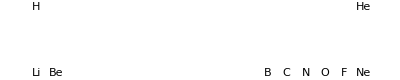

```mathematica
Graphics[Table[Text[ElementData[n,"Abbreviation"],{ElementData[n,"Group"],-ElementData[n,"Period"]}],{n,10}]]
```

2103/10/24

コードの説明:

Graphics[] -- グラフィクスオブジェクトを表示する

Text[] -- グラフィクスオブジェクト: Graphics[]内で扱えるオブジェクト

```mathematica
Graphics[a] (*エラー、表示されない*)
```

-Graphics-

```mathematica
Graphics[Text[a]] (*表示される*)
```

-Graphics-

```mathematica
Graphics[{Text[a,{0,0}],Text[b,{0,1}]}] (*座標指定による表示、複数のオブジェクトはリストでまとめる*)
```

-Graphics-

Table[] -- 要素の配列(多次元)をつくる

```mathematica
Table[i,{i,1,5}]
```

{1,2,3,4,5}

```mathematica
Table[{i,j},{i,1,5},{j,1,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3}},{{5,1},{5,2},{5,3}}}

周期表の説明(スライド:周期表.odp)

ElementData[] -- 元素のデータを取得する(インターネット接続の必要アリ)

```mathematica
ElementData[8]
```

Oxygen

```mathematica
ElementData[8,"Abbreviation"]
```

O

```mathematica
ElementData[8,"Group"] (*族が数値として返ってくる*)
```

16

```mathematica
ElementData[8,"Period"] (*周期が数値として返ってくる*)
```

2

```mathematica
{ElementData[8, "Group"], -ElementData[8, "Period"]} (*周期表における座標としてデータを取り出す*)
```

{16,-2}

式コピーのテクニック -- マルチプルクリック

```mathematica
Remove[f1,f2,f3,f4,y]
```

```mathematica
f1[f2[f3[f4[x]]]]
```

f1[f2[f3[f4[x]]]]

```mathematica
f1[f2[f3[f4[x,y]]]]
```

f1[f2[f3[f4[x,y]]]]

#### 配列系:数表:

```mathematica
TableForm[(worldShips=Sort[Cases[Map[{#,CountryData[#,"MerchantShips"]}&,CountryData[]],{_String,_Integer}],#1[[2]]>#2[[2]]&])[[{1,2,3,4,5}]],TableHeadings->{None,{"Country","Ships"}}]
```

Country | Ships
Panama | 6323
Liberia | 2204
China | 1826
Malta | 1438
Singapore | 1292

#### 配列系:数表: [ヒストグラム]

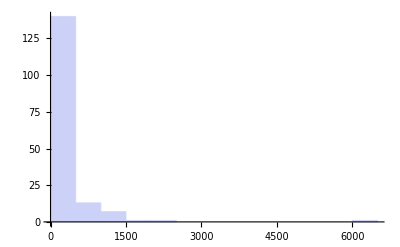

```mathematica
Histogram[Map[#[[2]]&,worldShips]]
```

#### 配列系:相関表: [隣接行列]

```mathematica
l=Range[20];
```

```mathematica
e={{1,2},{2,4},{10,12},{11,5},{12,6},{12,7},{13,6},{15,18},{16,4},{17,6}}
```

{{1,2},{2,4},{10,12},{11,5},{12,6},{12,7},{13,6},{15,18},{16,4},{17,6}}

```mathematica
Apply[UndirectedEdge,e,2]
```

{1<->2,2<->4,10<->12,11<->5,12<->6,12<->7,13<->6,15<->18,16<->4,17<->6}

```mathematica
g=Graph[l,Apply[UndirectedEdge,e,2]]
```

-Graphics-

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### 座標系:棒グラフ: [ヒストグラム]

#### 座標系:折れ線グラフ:

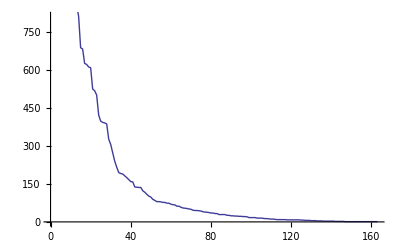

```mathematica
ListPlot[Map[#[[2]]&,worldShips],Joined->True]
```

#### 座標系:円グラフ

```mathematica
PieChart[Map[#[[2]]&,worldShips]]
```

-Graphics-

#### 座標系: [ベクトルプロット]

固有値、固有ベクトルの可視化

```mathematica
a[0] = {{2, 1}, {1, 3}}
```

{{2,1},{1,3}}

```mathematica
(clist = Table[{Cos[th], Sin[th]}, {th, Pi/12, 2 Pi, Pi/12}]) // Length
```

24

```mathematica
aDotclist = Map[a[0].# &, clist];
```

```mathematica
g1 = Graphics[{Map[Arrow[#] &, Transpose[{clist, aDotclist}]], Map[Arrow[{{0, 0}, #}] &, clist]}];
```

```mathematica
a["eigen"] = Eigensystem[a[0]]
```

{{1/2 (5+√5),1/2 (5-√5)},{{-3+1/2 (5+√5),1},{-3+1/2 (5-√5),1}}}

```mathematica
v = a["eigen"][[1]]*Map[Normalize[#] &, a["eigen"][[2]]];
```

```mathematica
g3 = Graphics[{Red, Map[Arrow[{{0, 0}, #}] &, v]}];
```

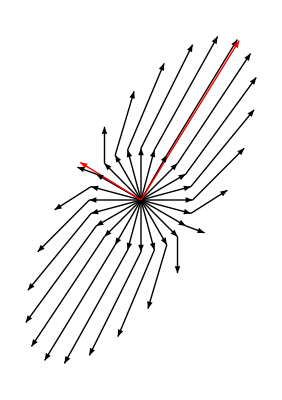

```mathematica
Show[g1, g3]
```

コードの説明:

固有値、固有ベクトルとは:
 A: 行列、x: ベクトル、λ: スカラーのとき、行列Aに対して、A.x = λ.x となる非ゼロのλ、xが求まる。
これは、行列Aによるベクトルの変換において、変換により単にλ倍されるベクトルが存在することを示す。

行列Aを次のように仮定する

```mathematica
a[0] = {{2, 1}, {1, 3}}
```

{{2,1},{1,3}}

行列によって変換されるベクトルを24個生成

```mathematica
(clist = Table[{Cos[th], Sin[th]}, {th, Pi/12, 2 Pi, Pi/12}]) // Length
```

24

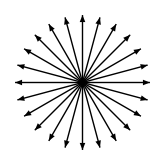

```mathematica
Graphics[Map[Arrow[{{0, 0}, #}] &, clist]]
```

24個のベクトルを行列A (a[0]) によって変換

```mathematica
aDotclist = Map[a[0].# &, clist];
```

「変換前のベクトル」と「そのベクトルの終点を始点とした変換後のベクトル」のグラフィクスオブジェクト(矢印表現)を生成

```mathematica
g1 = Graphics[{Map[Arrow[#] &, Transpose[{clist, aDotclist}]], Map[Arrow[{{0, 0}, #}] &, clist]}];
```

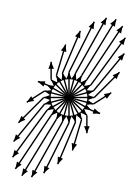

```mathematica
Graphics[g1]
```

行列A (a[0]) の固有値、固有ベクトルを求める

```mathematica
a["eigen"] = Eigensystem[a[0]]
```

{{1/2 (5+√5),1/2 (5-√5)},{{-3+1/2 (5+√5),1},{-3+1/2 (5-√5),1}}}

固有値*固有ベクトル、つまり、λ.x を求める

```mathematica
v = a["eigen"][[1]]*Map[Normalize[#] &, a["eigen"][[2]]];
```

ベクトル λ.x をグラフィクスオブジェクト(矢印表現:赤)として保存

```mathematica
g3 = Graphics[{Red, Map[Arrow[{{0, 0}, #}] &, v]}];
```

すべてのをグラフィクスオブジェクトを表示

```mathematica
Show[g1, g3]
```

-Graphics-

ベクトル {x,y} のベクトルプロット

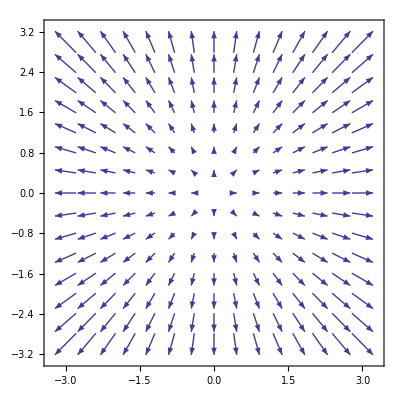

```mathematica
VectorPlot[{x, y}, {x, -3, 3}, {y, -3, 3}]
```

ベクトル {x,y} の行列 {{1,0,},{0,1}} による変換(変化無し)

```mathematica
VectorPlot[{{1,0},{0,1}}.{x, y}, {x, -3, 3}, {y, -3, 3}]
```

-Graphics-

ベクトル {x,y} の行列 {{0,1},{1,0}} による変換

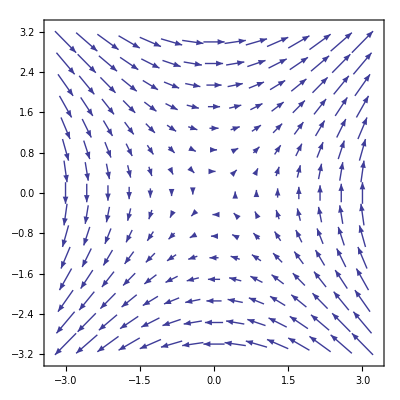

```mathematica
VectorPlot[{{0,1},{1,0}}.{x, y}, {x, -3, 3}, {y, -3, 3}]
```

ベクトル {x,y} の行列 a[0] による変換

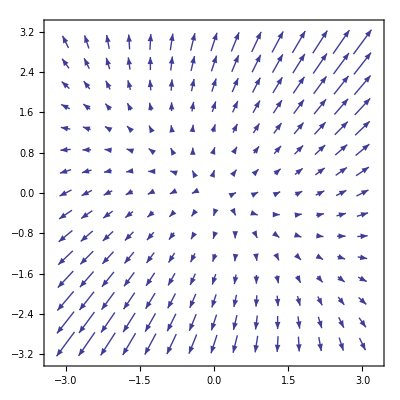

```mathematica
VectorPlot[a[0].{x, y}, {x, -3, 3}, {y, -3, 3}]
```

#### 座標系: [コンタープロット]

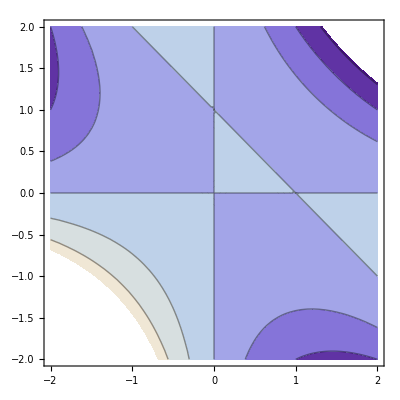

```mathematica
ContourPlot[x y (1-x-y),{x,-2,2},{y,-2,2}]
```

#### 座標系: [3Dプロット]

```mathematica
Plot3D[x y (1-x-y),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

#### 連結系:グラフ: [数式]

```mathematica
x={1,2,x}
```

{1,2,{1,2,2,{1,2,{1}}}}

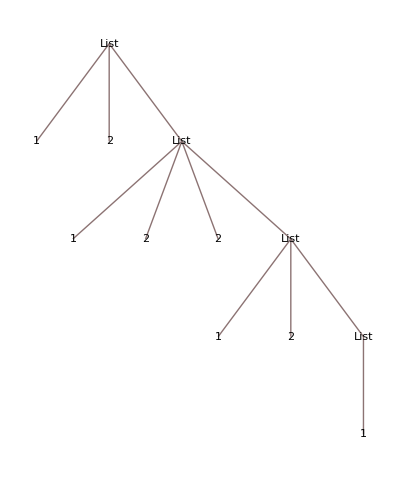

```mathematica
TreeForm[x]
```

#### 連結系:グラフ: [化学式]

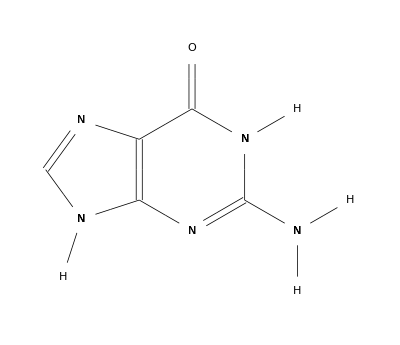

```mathematica
ChemicalData["Guanine"]
```

#### 連結系:グラフ: [崩壊図]

```mathematica
is = Select[IsotopeData[], 
   100 <= IsotopeData[#, "MassNumber"] <= 102 &];
```

```mathematica
isdata=
Map[Table[IsotopeData[#,pr],{pr,{"Symbol","DaughterNuclides"}}]&,is]
```

{{^100Kr,{Rubidium100}},{^100Rb,{Strontium100,Strontium99,Strontium98}},{^101Rb,{Strontium101,Strontium100}},{^102Rb,{Strontium102,Strontium101}},{^100Sr,{Yttrium100,Yttrium99}},{^101Sr,{Yttrium101,Yttrium100}},{^102Sr,{Yttrium102,Yttrium101}},{^100Y,{Zirconium100,Zirconium99}},{^101Y,{Zirconium101,Zirconium100}},{^102Y,{Zirconium102,Zirconium101}},{^100Zr,{Niobium100}},{^101Zr,{Niobium101}},{^102Zr,{Niobium102}},{^100Nb,{Molybdenum100}},{^101Nb,{Molybdenum101}},{^102Nb,{Molybdenum102}},{^100Mo,{Ruthenium100}},{^101Mo,{Technetium101}},{^102Mo,{Technetium102}},{^100Tc,{Ruthenium100,Molybdenum100}},{^101Tc,{Ruthenium101}},{^102Tc,{Ruthenium102}},{^100Ru,{}},{^101Ru,{}},{^102Ru,{}},{^100Rh,{Ruthenium100}},{^101Rh,{Ruthenium101}},{^102Rh,{Ruthenium102,Palladium102}},{^100Pd,{Rhodium100}},{^101Pd,{Rhodium101}},{^102Pd,{Ruthenium102}},{^100Ag,{Palladium100}},{^101Ag,{Palladium101}},{^102Ag,{Palladium102}},{^100Cd,{Silver100}},{^101Cd,{Silver101}},{^102Cd,{Silver102}},{^100In,{Cadmium100,Silver99}},{^101In,{Cadmium101,Silver100}},{^102In,{Cadmium102,Silver101}},{^100Sn,{Indium100,Cadmium99}},{^101Sn,{Indium101,Cadmium100}},{^102Sn,{Indium102,Cadmium101}}}

```mathematica
isr=Flatten[Map[Outer[List, {#[[1]]}, #[[2]]] &, isdata],2]
```

{{^100Kr,Rubidium100},{^100Rb,Strontium100},{^100Rb,Strontium99},{^100Rb,Strontium98},{^101Rb,Strontium101},{^101Rb,Strontium100},{^102Rb,Strontium102},{^102Rb,Strontium101},{^100Sr,Yttrium100},{^100Sr,Yttrium99},{^101Sr,Yttrium101},{^101Sr,Yttrium100},{^102Sr,Yttrium102},{^102Sr,Yttrium101},{^100Y,Zirconium100},{^100Y,Zirconium99},{^101Y,Zirconium101},{^101Y,Zirconium100},{^102Y,Zirconium102},{^102Y,Zirconium101},{^100Zr,Niobium100},{^101Zr,Niobium101},{^102Zr,Niobium102},{^100Nb,Molybdenum100},{^101Nb,Molybdenum101},{^102Nb,Molybdenum102},{^100Mo,Ruthenium100},{^101Mo,Technetium101},{^102Mo,Technetium102},{^100Tc,Ruthenium100},{^100Tc,Molybdenum100},{^101Tc,Ruthenium101},{^102Tc,Ruthenium102},{^100Rh,Ruthenium100},{^101Rh,Ruthenium101},{^102Rh,Ruthenium102},{^102Rh,Palladium102},{^100Pd,Rhodium100},{^101Pd,Rhodium101},{^102Pd,Ruthenium102},{^100Ag,Palladium100},{^101Ag,Palladium101},{^102Ag,Palladium102},{^100Cd,Silver100},{^101Cd,Silver101},{^102Cd,Silver102},{^100In,Cadmium100},{^100In,Silver99},{^101In,Cadmium101},{^101In,Silver100},{^102In,Cadmium102},{^102In,Silver101},{^100Sn,Indium100},{^100Sn,Cadmium99},{^101Sn,Indium101},{^101Sn,Cadmium100},{^102Sn,Indium102},{^102Sn,Cadmium101}}

```mathematica
isrl=Map[Rule[#[[1]],IsotopeData[#[[2]],"Symbol"]]&,isr]
```

{^100Kr→^100Rb,^100Rb→^100Sr,^100Rb→^99Sr,^100Rb→^98Sr,^101Rb→^101Sr,^101Rb→^100Sr,^102Rb→^102Sr,^102Rb→^101Sr,^100Sr→^100Y,^100Sr→^99Y,^101Sr→^101Y,^101Sr→^100Y,^102Sr→^102Y,^102Sr→^101Y,^100Y→^100Zr,^100Y→^99Zr,^101Y→^101Zr,^101Y→^100Zr,^102Y→^102Zr,^102Y→^101Zr,^100Zr→^100Nb,^101Zr→^101Nb,^102Zr→^102Nb,^100Nb→^100Mo,^101Nb→^101Mo,^102Nb→^102Mo,^100Mo→^100Ru,^101Mo→^101Tc,^102Mo→^102Tc,^100Tc→^100Ru,^100Tc→^100Mo,^101Tc→^101Ru,^102Tc→^102Ru,^100Rh→^100Ru,^101Rh→^101Ru,^102Rh→^102Ru,^102Rh→^102Pd,^100Pd→^100Rh,^101Pd→^101Rh,^102Pd→^102Ru,^100Ag→^100Pd,^101Ag→^101Pd,^102Ag→^102Pd,^100Cd→^100Ag,^101Cd→^101Ag,^102Cd→^102Ag,^100In→^100Cd,^100In→^99Ag,^101In→^101Cd,^101In→^100Ag,^102In→^102Cd,^102In→^101Ag,^100Sn→^100In,^100Sn→^99Cd,^101Sn→^101In,^101Sn→^100Cd,^102Sn→^102In,^102Sn→^101Cd}

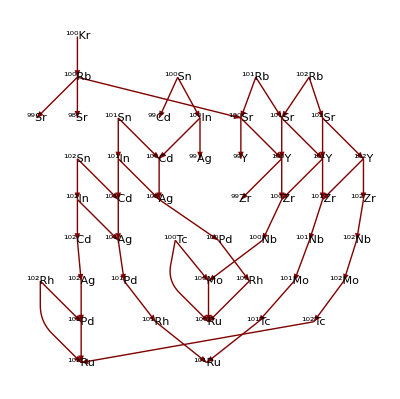

```mathematica
LayeredGraphPlot[
isrl, 
 DirectedEdges -> True, VertexLabeling -> True]
```

#### 領域系:地図: [世界地図]

いいかげんな世界地図(より正確な座標も持っている)

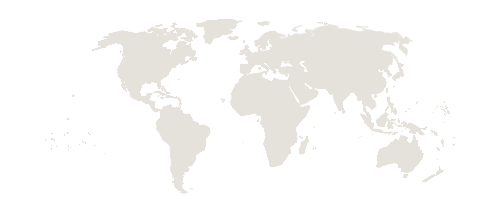

```mathematica
CountryData["World","Shape"]
```

```mathematica
coordsToXYZ[list_] := 
  Transpose[{Cos[#[[1]]]*Cos[#[[2]]], Cos[#[[1]]]*Sin[#[[2]]], 
      Sin[#[[1]]]} &@Reverse@Transpose[list*Pi/180.]];
```

```mathematica
coord3DWorld=Map[coordsToXYZ[#]&,CountryData["World","Shape"][[1]][[3]][[1]],{1}];
```

```mathematica
Graphics3D[Polygon[coord3DWorld]]
```

-Graphics3D-

#### 解析法と表示法は表裏一体(補間・スムージング)

##### 補間

```mathematica
??ListInterpolation
```

ListInterpolation[array] 与えられた値の配列を補間する近似関数を表すInterpolatingFunctionオブジェクトを作成する．
ListInterpolation[array,{{x_min,x_max},{y_min,y_max},…}] array  の各値の座標を決めるグリッド域を指定する．

Attributes[ListInterpolation]={Protected}
 
Options[ListInterpolation]={InterpolationOrder→3,Method→Automatic,PeriodicInterpolation→False}

##### 畳み込み

```mathematica
??Convolve
```

RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "]"}] 式 StyleBox["f", "TI"]と StyleBox["g", "TI"] の StyleBox["x", "TI"] についてのたたみ込みを返す．
RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 多次元たたみ込みを返す．

Attributes[Convolve]={Protected,ReadProtected}

たたみ込みは一般に関数を滑らかにする：

```mathematica
f0=UnitBox[t0]; (*もとの関数*)
```

```mathematica
f1=Convolve[f0,f0,t0,t1] (*一回畳み込み*)
```

UnitTriangle[t1]

```mathematica
f2=Convolve[f1,f1,t1,t2] (*2回畳み込み*)
```

Piecewise[{{1/6 (4-6 t2^2-3 t2^3), -1<t2<0}, {1/6 (-6 t2-6 t2^2-t2^3), t2==-1}, {1/6 (8-12 t2+6 t2^2-t2^3), 1<t2<2}, {1/3 (2-3 t2+t2^3), t2==0}, {1/6 (6 t2-6 t2^2+t2^3), t2==1}, {1/6 (8+12 t2+6 t2^2+t2^3), -2<t2<-1}, {1/6 (4-6 t2^2+3 t2^3), 0<t2<1}, {0, True}}]

```mathematica
f3=Convolve[f2,f2,t2,t3]; (*3回畳み込み*)
```

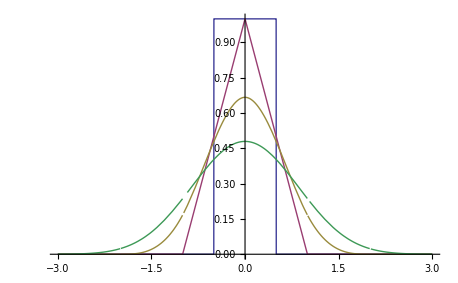

```mathematica
Plot[Evaluate[{f0,f1,f2,f3}/.{t0->x,t1->x,t2->x,t3->x}],{x,-3,3}]
```

```mathematica
Integrate[(f0/.t0->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f1/.t1->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f2/.t2->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f3/.t3->x),{x,-Infinity,Infinity}]
```

1

```mathematica
??ListConvolve
```

ListConvolve[ker,list] 核 ker と list のたたみ込みを形成する．
ListConvolve[ker,list,k] ker の k 次の要素がlist の各要素と揃えられる循環たたみ込みを形成する．
ListConvolve[ker,list,{k_L,k_R}] 最初の要素が list[[1]] ker[[k_L]]を含み，最後の要素が list[[-1]] ker[[k_R]]を含む循環たたみ込みを形成する．
ListConvolve[ker,list,klist,p] list の最後が要素 p の反復で充填されるような，たたみ込みを形成する．
ListConvolve[ker,list,klist,{p_1,p_2,…}] list の最後が p_i で循環反復充填されるたたみ込みを形成する．
ListConvolve[ker,list,klist,padding,g,h] g がTimesの代りに，h がPlusの代りに使われる一般化されたたたみ込みを形成する．
ListConvolve[ker,list,klist,padding,g,h,lev] ker と list でレベル lev の要素を使い，たたみ込みを形成する．

Attributes[ListConvolve]={Protected}

自分自身のリスト畳み込み:

```mathematica
Partition[Array[a,10],3,1]
```

{{a[1],a[2],a[3]},{a[2],a[3],a[4]},{a[3],a[4],a[5]},{a[4],a[5],a[6]},{a[5],a[6],a[7]},{a[6],a[7],a[8]},{a[7],a[8],a[9]},{a[8],a[9],a[10]}}

```mathematica
Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]
```

{{a[3],a[2],a[1]},{a[4],a[3],a[2]},{a[5],a[4],a[3]},{a[6],a[5],a[4]},{a[7],a[6],a[5]},{a[8],a[7],a[6]},{a[9],a[8],a[7]},{a[10],a[9],a[8]}}

```mathematica
Partition[Array[a,10],3,1]*Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]
```

{{a[1] a[3],a[2]^2,a[1] a[3]},{a[2] a[4],a[3]^2,a[2] a[4]},{a[3] a[5],a[4]^2,a[3] a[5]},{a[4] a[6],a[5]^2,a[4] a[6]},{a[5] a[7],a[6]^2,a[5] a[7]},{a[6] a[8],a[7]^2,a[6] a[8]},{a[7] a[9],a[8]^2,a[7] a[9]},{a[8] a[10],a[9]^2,a[8] a[10]}}

```mathematica
Map[Tr[#]&,Partition[Array[a,10],3,1]*Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]]
```

{a[2]^2+2 a[1] a[3],a[3]^2+2 a[2] a[4],a[4]^2+2 a[3] a[5],a[5]^2+2 a[4] a[6],a[6]^2+2 a[5] a[7],a[7]^2+2 a[6] a[8],a[8]^2+2 a[7] a[9],a[9]^2+2 a[8] a[10]}

課題: 上記をひとつの関数にまとめてみよう。

2013/10/31

注意: 畳み込みは、一般的に、対象となる関数、および、カーネルとなる関数が返す値の範囲が、0 ≤ f(x) ≤ 1。
さらに、畳み込み前と畳み込み後において、マイナス無限大からプラス無限大の積分が1となるように調整できれば扱いやすい。

```mathematica
1/6 (8-12 t2+6 t2^2-t2^3)/.t2->10
```

-256/3

##### 移動平均

```mathematica
??MovingAverage
```

MovingAverage[list,r] r 個の要素を平均することで計算した list の移動平均を返す．
MovingAverage[list,{w_1,w_2,…,w_r}] 重み w_i で計算した list の移動平均を返す．

Attributes[MovingAverage]={Protected,ReadProtected}

##### フィッテイング

```mathematica
??Fit
```

Fit[data,funs,vars] 変数 vars の関数 funs の線形な組合せで，与えられたデータの最小二乗法フィットを行う．

Attributes[Fit]={Protected}

```mathematica
l1=Table[n+RandomReal[{-1,1}],{n,20}]
```

{1.77847,2.40703,3.75922,3.76019,5.47608,6.01325,6.21187,7.34968,8.2711,9.14559,10.8581,12.3371,13.2659,14.1694,14.1663,16.3901,17.6836,18.8847,18.5385,20.8971}

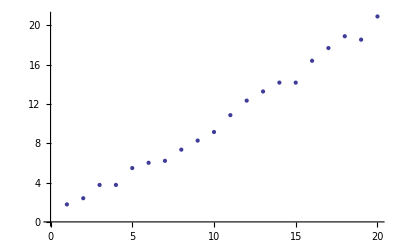

```mathematica
ListPlot[l1]
```

```mathematica
Fit[l1,{x},x]
```

1.00638 x

```mathematica
Fit[l1,{1,x},x]
```

0.004993+1.00602 x

```mathematica
Fit[l1,{1,x,x^2},x]
```

0.933295+0.752843 x+0.0120559 x^2

### 提出課題

1. オシロスコープから得たデータをそのままプロットせよ

2. 1のデータを滑らかにしてプロットせよ(レンジ等に気をつけること)

## 4.探索的データ解析

### モデル

#### 準備

n次モーメント: Integrate[x^n f[x],dx] ; これは、y = f[x]としたときの、y軸に対するモーメントである。

n次平滑値(天野による定義、n次モーメントの値を0次モーメントの値で割ったもの): Integrate[x^n f[x],dx] / Integrate[f[x],dx]

確率分布の0次モーメントは1である。

度数分布の0次モーメント(表現がヘンだが)はサンプル総数である。

したがって、1次平滑値は平均値となる。

#### 確率密度関数 (PDF: Probability Density Function)

pdfの-無限大から+無限大までの積分が1。

すべての区間で負の値をとらない。

```mathematica
??PDF
```

PDF[dist,x] x で評価された記号分布 dist についての確率密度関数(PDF)を返す．
PDF[dist,{x_1,x_2,…}] {x_1,x_2,…}で評価された記号分布 dist についての多変量確率密度関数を返す．
PDF[dist] 確率密度関数を純関数として返す．

Attributes[PDF]={Protected,ReadProtected}

```mathematica
PDF[NormalDistribution[0, 1], x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}]
```

1

#### 累積分布関数 (CDF: Cumulative Distribution Function)

cdf(x) =∫_(-∞)^x pdf(t)ⅆt

```mathematica
??CDF
```

CDF[dist,x] x で評価された記号分布 dist の累積分布関数を返す．
CDF[dist,{x_1,x_2,…}] {x_1,x_2,…}で評価された記号分布 dist についての多変量累積分布関数を返す．
CDF[dist] CDFを純関数として返す．

Attributes[CDF]={Protected,ReadProtected}

```mathematica
CDF[NormalDistribution[0,1],x]
```

1/2 Erfc[-x/(√2)]

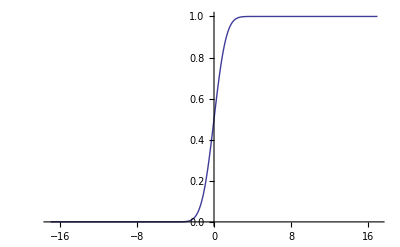

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

#### 二重指数関数

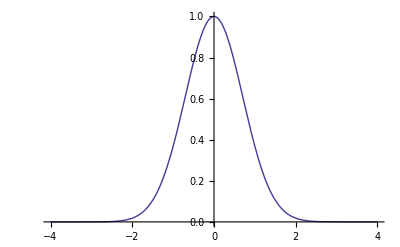

```mathematica
Plot[E^-(x^2),{x,-4,4}]
```

```mathematica
Integrate[E^-(x^2),{x,-Infinity,Infinity}]
```

√π

```mathematica
Integrate[E^-(-m+x^2),{x,-Infinity,Infinity}]
```

ⅇ^m √π

```mathematica
Integrate[E^-((-m+x^2)/(2s^2)),{x,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(m/(2 s^2)) √(2 π))/(√(1/s^2)),Re[s^2]>0]

```mathematica
Solve[D[D[E^-(s^2 x^2),x],x]==0,{x}]
```

{{x→-1/(√2 s)},{x→1/(√2 s)}}

#### 正規分布

正規分布の式、m:平均、s:標準偏差

```mathematica
PDF[NormalDistribution[m,s], x]
```

(ⅇ^(-(-m+x)^2/(2 s^2)))/(√(2 π) s)

正規分布の形

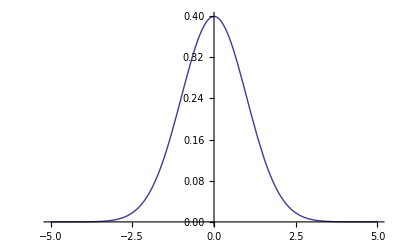

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5}]
```

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}]
```

1

1次モーメント / 0次モーメントは平均と一致する

```mathematica
Integrate[x PDF[NormalDistribution[m,1],x],{x,-Infinity,Infinity}]
```

m

```mathematica
Integrate[x PDF[NormalDistribution[m,4],x],{x,-Infinity,Infinity}]
```

m

2次モーメントは分散と一致する(平均がゼロの場合)

```mathematica
Integrate[x^2 PDF[NormalDistribution[0,2],x],{x,-Infinity,Infinity}]
```

4

```mathematica
Integrate[x^2 PDF[NormalDistribution[0,3],x],{x,-Infinity,Infinity}]
```

9

(x - mean(x))に対する2次モーメントは分散と一致する

```mathematica
Integrate[x^2 PDF[NormalDistribution[4,3],x],{x,-Infinity,Infinity}]
```

25

```mathematica
Integrate[(x-4)^2 PDF[NormalDistribution[4,3],x],{x,-Infinity,Infinity}]
```

9

関数 CentralMoment[] は平均に対するn次モーメントを与える

```mathematica
CentralMoment[NormalDistribution[0,3],2]
```

9

```mathematica
CentralMoment[NormalDistribution[4,3],2]
```

9

正規分布の歪度(3次モーメント/2次モーメント^(3/2))は0

```mathematica
Skewness[NormalDistribution[0,1]]
```

0

正規分布の尖度(4次モーメント/2次モーメント^2)は3

```mathematica
Kurtosis[NormalDistribution[0,1]]
```

3

変曲点は、平均値±標準偏差の値と一致する

```mathematica
Solve[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{x→m-s},{x→m+s}}

```mathematica
Reduce[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

s≠0&&(x==m+s||x==m-s)

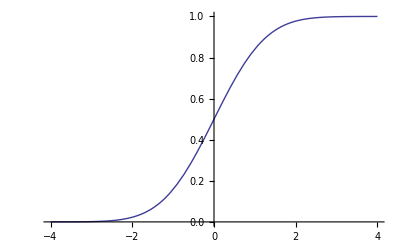

```mathematica
Plot[CDF[NormalDistribution[0,1], x]/.{x->t},{t,-4,4}]
```

#### その他の分布

Zipf分布

下記は、データのサイズが4の場合のランクが1から4位までの生産量比

```mathematica
PDF[ZipfDistribution[4, 1], {1, 2, 3, 4}] // N
```

```mathematica
zipf[rank_,a_,c_]:=c*rank^(-a)
```

```mathematica
fitargs=FindFit[Map[#[[2]]&,worldShips],zipf[rank,a,c],{a,c},rank]
```

{a→0.929126,c→5963.12}

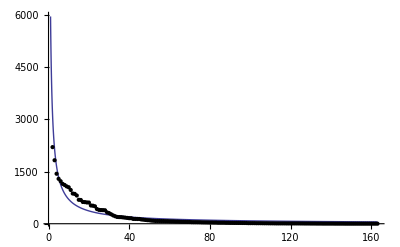

```mathematica
Plot[zipf[rank,a,c]/.fitargs,{rank,1,Length[worldShips]},Epilog->MapIndexed[Point[Flatten[{#2,#1[[2]]}]]&,worldShips],PlotRange->All]
```

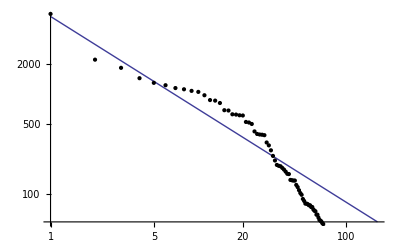

```mathematica
gobjLLP=LogLogPlot[zipf[rank,a,c]/.fitargs,{rank,1,Length[worldShips]},Epilog->MapIndexed[Point[Flatten[{Log[#2],Log[#1[[2]]]}]]&,worldShips]]
```

OrlovとChitashviliによれば、Zipf族の関数はつぎの定義のように一般化できる

```mathematica
orlovZ[m]:=Integrate[(Log[1+x]^(γ-1) x^α)/((1+x)^(m+1) (1+x)^β),{x,0,Infinity}]/Integrate[(Log[1+x]^(γ-1) x^(α-1))/((1+x)^(β+1)),{x,0,Infinity}]
```

```mathematica
orlovZ[m]
```

(∫_0^∞ x^α (1+x)^(-1-m-β) Log[1+x]^(-1+γ)ⅆx)/(∫_0^∞ x^(-1+α) (1+x)^(-1-β) Log[1+x]^(-1+γ)ⅆx)

Zipfの法則

```mathematica
orlovZ[m]/.{α->1,β->1,γ->1}
```

ConditionalExpression[1/(m+m^2),Re[m]>0]

Yuleの法則

```mathematica
orlovZ[m] /. {β -> α, γ -> 1}
```

ConditionalExpression[(α Gamma[m] Gamma[1+α])/Gamma[1+m+α],Re[α]>0&&Re[m]>0]

Yule-Simonの法則

```mathematica
orlovZ[m]/.{α->1,γ->1}
```

ConditionalExpression[β/((-1+m+β) (m+β)),Re[β]>0&&Re[m+β]>1]

### ランダムネス

一様乱数

```mathematica
ra=Table[Random[],{400}];
```

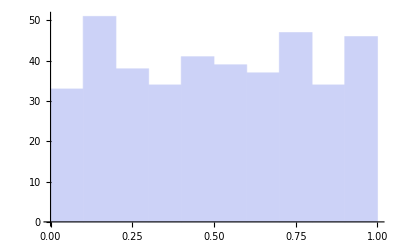

```mathematica
Histogram[ra]
```

一様乱数から分布を作る -変換法-

分布の積分の逆関数を求めることができれば、あるいは、解析的にその値を得ることができれば変換法により一様乱数から、特定の分布を得られる。

--CDF--

```mathematica
CDF[NormalDistribution[0,1]]//FullForm
```

Function[Times[Erfc[Times[Plus[0,Times[-1,Slot[1]]],Power[Times[Sqrt[2],1],-1]]],Power[2,-1]]]

```mathematica
Plot[(1/2 Erfc[(0-#1)/(√2 1)]&)[x],{x,-16.970562748477143,16.970562748477143}]
```

-Graphics-

```mathematica
ifc:=InverseFunction[CDF[NormalDistribution[0,1]]]
```

```mathematica
ira=Map[ifc[#//N]&,ra];
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

General::stop: この計算中に，InverseFunction :: ifunのこれ以上の出力は表示されません．

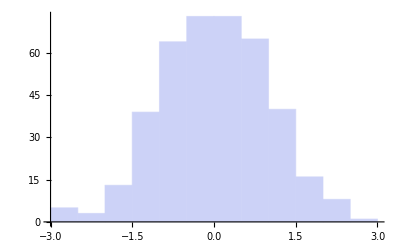

```mathematica
Histogram[ira]
```

--PDF-- (積分のステップが必要)

```mathematica
PDF[NormalDistribution[0, 1]]
```

Exp[-1/2 ((#1-0) 1/1)^2]/(1 √(2 π))&

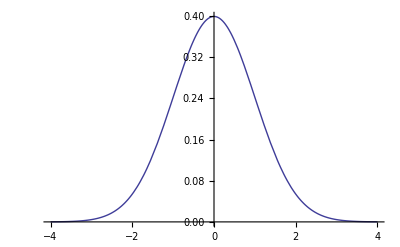

```mathematica
Plot[(Exp[-1/2 ((#1-0) 1/1)^2]/(1 √(2 π))&)[x],{x,-4,4}]
```

```mathematica
Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]
```

1/2 (1+Erf[t/(√2)])

```mathematica
Function[Evaluate[Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]/.t->#]]
```

1/2 (1+Erf[#1/(√2)])&

```mathematica
Plot[(1/2 (1+Erf[#1/(√2)])&)[x],{x,-16.970562748477143,16.970562748477143}]
```

-Graphics-

```mathematica
ifp:=InverseFunction[Function[Evaluate[Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]/.t->#]]]
```

```mathematica
ifp[0.2]
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

-0.841621

```mathematica
ira=Map[ifp[#//N]&,ra];
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

General::stop: この計算中に，InverseFunction :: ifunのこれ以上の出力は表示されません．

```mathematica
ira[[1]]
```

-0.212023

```mathematica
Histogram[ira,10]
```

-Graphics-

### 探索的データ解析

スライド:知識構造化法_中山先生-天野改.odp

```mathematica
??Median
```

Median[list] list の要素の中央値を与える．
Median[dist] 記号分布 dist の中央値を与える．

Attributes[Median]={Protected,ReadProtected}

```mathematica
(*最頻値*)??Commonest
```

RowBox[{"Commonest", "[", StyleBox["list", "TI"], "]"}] StyleBox["list", "TI"] 中の最も一般的な要素のリストを与える．
RowBox[{"Commonest", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] StyleBox["list", "TI"] 中の最も一般的な StyleBox["n", "TI"] 個の要素のリストを与える．

Attributes[Commonest]={Protected,ReadProtected}

```mathematica
??Quantile
```

Quantile[list,q] list の q 分位数を与える．
Quantile[list,{q_1,q_2,…}] 分位数 q_1, q_2, …のリストを与える．
Quantile[list,q,{{a,b},{c,d}}] パラメータ a，b，c，d で指定された分位数の定義を使う．
Quantile[dist,q] 記号分布 dist の分位数を与える．

Attributes[Quantile]={Protected,ReadProtected}

```mathematica
??BoxWhiskerChart
```

BoxWhiskerChart[{x_1,x_2,…}] 値  x_iの箱ひげ図を作成する．
BoxWhiskerChart[{x_1,x_2,…},bwspec] 記号指定 bwspec による箱ひげ図を作成する．
BoxWhiskerChart[{data_1,data_2,…},…] 各 data_iの記号による箱ひげ図を作成する．
BoxWhiskerChart[{{data_1,data_2,…},…},…] 複数のデータ集合{data_1,data_2,…}から箱ひげ図を作成する．

Attributes[BoxWhiskerChart]={Protected,ReadProtected}

#### 分布モデルとの対応

正規分布プロットに対する幹葉表示

平均値に対する中央値

標準偏差に対するヒンジ散布度(上ヒンジ値と下ヒンジ値の差をヒンジ散布度と言い、これを1.35で割った値を擬似標準偏差と言う)

## 5.様々な類似度・距離の考え方

## 6.非階層的クラスタリング

## 7.階層的クラスタリング

## 8.自己組織化マップ

### ニューラルネットワーク

#### ニューロン

加算器

```mathematica
adder[o_List,w_List]:=Tr[w*o]
```

```mathematica
adder[{1,2,3},{a,b,c}]
```

a+2 b+3 c

入出力関数 -シグモイド関数-

```mathematica
SGM[a_,th_]:=1/(1+E^(-a+th))
```

```mathematica
Plot3D[SGM[in,t],{in,-10,10},{t,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

ニューロンの設計

```mathematica
NER[o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],th]>=th,1,0]
```

```mathematica
ner[o_List,w_List,iofunc_,th_]:=iofunc[adder[o,w],th]
```

加算器と入出力関数(iofunc)を組み合わせニューロンを作る。
入出力関数(iofunc)は、いま、シグモイド(0 < SGM < 1)に定義されている。
かつ、ニューロン(NER)は、非線形活性化関数として機能している。
しきい値 th は、iofunc() そのものにも影響するかたちになっている。

設計したニューロンの性質:

入力を{1,1,1}、重みを{10,10,10}とする。

当然ながら、thに1より大きい値を設定すると、ニューロンの出力は、かならず 0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

当然ながら、thに0より小さい値を設定すると、ニューロンの出力は、かならず 1。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

つまり、シグモイドを採る理由は、しきい値の範囲を決めるため、と解釈してもよい。

次に、重みをすべて負の値とし、thを0 <= th <= 1の間で変化させる。thが0の場合のみ、ニューロンの出力は1。

```mathematica
Table[{NER[{1,1,1},{-1,-1,-1},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

重みをすべて大きな正の値とし、thを0 <= th <= 1の間で変化させる。thが1に非常に近い場合にのみ、ニューロンの出力は0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.

#### 教師あり学習

ニューラルネットワークの簡単な例:

-Graphics-

学習データ: {<入力ベクトル>,<期待される出力>}

```mathematica
ldata1={
{{0,0},0},
{{1,0},0},
{{0,1},0},
{{1,1},1}
}
```

{{{0,0},0},{{1,0},0},{{0,1},0},{{1,1},1}}

```mathematica
TableForm[Map[Flatten[#]&,ldata1],TableHeadings->{Table[n,{n,4}],{"入力１","入力２","出力(期待)"}}]
```

| 入力１ | 入力２ | 出力(期待)
1 | 0 | 0 | 0
2 | 1 | 0 | 0
3 | 0 | 1 | 0
4 | 1 | 1 | 1

重みベクトル、しきい値の初期値

```mathematica
wdata[0]={1.5,-1.0}
```

{1.5,-1.}

```mathematica
thh[0]=0.8
```

0.8

```mathematica
NER[ldata1[[1,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[2,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[3,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0

上の例では、パターン4のときに期待する値が得られていない。

学習:

重みとしきい値を変化させ、学習をおこなう。

しきい値を小さくすれば、出力は大きくなる。

```mathematica
delta=.
```

```mathematica
thh[0]
```

0.8

```mathematica
ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0.425557

```mathematica
delta[1]=ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]-thh[0]
```

-0.374443

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]+delta[1]]
```

1

入力に対応する重みを大きくすれば、出力は大きくなる。

```mathematica
wdata[0]
```

{1.5,-1.}

```mathematica
NER[ldata1[[4,1]],wdata[0]+0.5*ldata1[[4,1]],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0]+(0.5+0.5)*ldata1[[4,1]],SGM,thh[0]]
```

1

入力がない場合、しきい値を変化させ、入力がある場合、それに対応する重みを変化させることによって学習を行う。どの程度変化させるか -> デルタルールなど。

#### 分類機械と競合学習

分類機械:入力のパターンを出力の個数に分類する。出力の受ける入力の重みの総和は1。

-Graphics-

∑ w_i,1 = 1 ; ∑ w_i,2 = 1

競合学習の手順:

重みの初期値:

```mathematica
wmat[0]={
{0.5,0.5},
{0.6,0.4}
}
```

{{0.5,0.5},{0.6,0.4}}

```mathematica
TableForm[wmat[0],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.6 | 0.4

入力パターン:

```mathematica
pdata1={
{1,0},
{0,1},
{1,1},
{1,0}
}
```

{{1,0},{0,1},{1,1},{1,0}}

```mathematica
TableForm[pdata1,TableHeadings->{Table[i,{i,4}],{"入力1","入力2"}}]
```

| 入力1 | 入力2
1 | 1 | 0
2 | 0 | 1
3 | 1 | 1
4 | 1 | 0

勝者に対する重みの変化量:
dw = l (c/n - w) ; l : 学習率、c : 入力値、n : 入力数、w : 現在の重み

学習係数 lを0.5に。

```mathematica
l=0.5
```

0.5

入力パターン1に対して学習:

入力パターン1の場合の出力1:

```mathematica
pdata1[[1]] wmat[0][[1]]//Tr
```

0.5

入力パターン1の場合の出力2:

```mathematica
pdata1[[1]] wmat[0][[2]]//Tr
```

0.6

出力2が勝者となる

そこで、w_2,1とw_2,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.6 | 0.4

```mathematica
dw[1][1,1]=0
```

0

```mathematica
dw[1][1,2]=0
```

0

まず、wd_2,1(出力2入力1)

pdata1[[1,1]] : パターン1:入力1
Tr[pdata1[[1]]] : パターン1:出力2への入力数
wmat[0][[2,1]] : パターン1:出力2、入力1のとき

```mathematica
dw[1][2,1]=l(pdata1[[1,1]]/Tr[pdata1[[1]]]-wmat[0][[2,1]])
```

0.2

つぎに、wd_2,2(出力2入力2)

pdata1[[1,2]] : パターン1:入力2
Tr[pdata1[[1]]] : パターン1:出力2への入力数
wmat[0][[2,2]] : パターン1:出力2、入力2のとき

```mathematica
dw[1][2,2]=l(pdata1[[1,2]]/Tr[pdata1[[1]]]-wmat[0][[2,2]])
```

-0.2

重みを更新:

```mathematica
wmat[0]
```

{{0.5,0.5},{0.6,0.4}}

```mathematica
wmat[1]=wmat[0]+{{dw[1][1,1],dw[1][1,2]},{dw[1][2,1],dw[1][2,2]}}
```

{{0.5,0.5},{0.8,0.2}}

```mathematica
TableForm[wmat[1],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

入力パターン2に対して学習:

入力パターン2の場合の出力1:

```mathematica
pdata1[[2]] wmat[1][[1]]//Tr
```

0.5

入力パターン1の場合の出力2:

```mathematica
pdata1[[2]] wmat[1][[2]]//Tr
```

0.2

出力1が勝者となる

そこで、w_1,1とw_1,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

```mathematica
dw[2][2,1]=0
```

0

```mathematica
dw[2][2,2]=0
```

0

まず、wd_1,1(出力1入力1)

pdata1[[2,1]] : パターン2:入力1
Tr[pdata1[[2]]] : パターン2:出力1への入力数
wmat[1][[1,1]] : パターン2:出力1、入力1のとき

```mathematica
dw[2][1,1]=l(pdata1[[2,1]]/Tr[pdata1[[2]]]-wmat[1][[1,1]])
```

-0.25

つぎに、wd_1,2(出力1入力2)

pdata1[[2,2]] : パターン2:入力2
Tr[pdata1[[2]]] : パターン2:出力1への入力数
wmat[1][[1,2]] : パターン2:出力1、入力2のとき

```mathematica
dw[2][1,2]=l(pdata1[[2,2]]/Tr[pdata1[[2]]]-wmat[1][[1,2]])
```

0.25

重みを更新:

```mathematica
wmat[1]
```

{{0.5,0.5},{0.8,0.2}}

```mathematica
wmat[2]=wmat[1]+{{dw[2][1,1],dw[2][1,2]},{dw[2][2,1],dw[2][2,2]}}
```

{{0.25,0.75},{0.8,0.2}}

```mathematica
TableForm[wmat[2],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.25 | 0.75
出力2 | 0.8 | 0.2

入力パターン3に対して学習:

入力パターン3の場合の出力1:

```mathematica
pdata1[[3]] wmat[2][[1]]//Tr
```

1.

入力パターン3の場合の出力2:

```mathematica
pdata1[[3]] wmat[2][[2]]//Tr
```

1.

双方を勝者として学習させる。

そこで、w_1,1とw_1,2、w_2,1とw_2,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

まず、wd_1,1(出力1入力1)

pdata1[[3,1]] : パターン3:入力1
Tr[pdata1[[3]]] : パターン3:出力1への入力数
wmat[2][[1,1]] : パターン3:出力1、入力1のとき

```mathematica
dw[3][1,1]=l(pdata1[[3,1]]/Tr[pdata1[[3]]]-wmat[2][[1,1]])
```

0.125

つぎに、wd_1,2(出力1入力2)

pdata1[[3,2]] : パターン3:入力2
Tr[pdata1[[3]]] : パターン3:出力1への入力数
wmat[2][[1,2]] : パターン3:出力1、入力2のとき

```mathematica
dw[3][1,2]=l(pdata1[[3,2]]/Tr[pdata1[[3]]]-wmat[2][[1,2]])
```

-0.125

つぎに、wd_2,1(出力2入力1)

pdata1[[3,1]] : パターン3:入力1
Tr[pdata1[[3]]] : パターン3:出力2への入力数
wmat[2][[2,1]] : パターン3:出力2、入力1のとき

```mathematica
dw[3][2,1]=l(pdata1[[3,1]]/Tr[pdata1[[3]]]-wmat[2][[2,1]])
```

-0.15

つぎに、wd_2,2(出力2入力2)

pdata1[[3,2]] : パターン3:入力2
Tr[pdata1[[3]]] : パターン3:出力2への入力数
wmat[2][[2,2]] : パターン3:出力2、入力2のとき

```mathematica
dw[3][2,2]=l(pdata1[[3,2]]/Tr[pdata1[[3]]]-wmat[2][[2,2]])
```

0.15

重みを更新:

```mathematica
wmat[2]
```

{{0.25,0.75},{0.8,0.2}}

```mathematica
wmat[3]=wmat[2]+{{dw[3][1,1],dw[3][1,2]},{dw[3][2,1],dw[3][2,2]}}
```

{{0.375,0.625},{0.65,0.35}}

```mathematica
TableForm[wmat[3],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.65 | 0.35

入力パターン4に対して学習:

入力パターン4の場合の出力1:

```mathematica
pdata1[[4]] wmat[3][[1]]//Tr
```

0.375

入力パターン4の場合の出力2:

```mathematica
pdata1[[4]] wmat[3][[2]]//Tr
```

0.65

出力2が勝者となる。

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.65 | 0.35

そこで、w_2,1とw_2,2を変化させる。

```mathematica
dw[4][1,1]=0
```

0

```mathematica
dw[4][1,2]=0
```

0

まず、wd_2,1(出力2入力1)

pdata1[[4,1]] : パターン4:入力1
Tr[pdata1[[4]]] : パターン4:出力2への入力数
wmat[3][[2,1]] : パターン4:出力2、入力1のとき

```mathematica
dw[4][2,1]=l(pdata1[[4,1]]/Tr[pdata1[[4]]]-wmat[3][[2,1]])
```

0.175

つぎに、wd_2,2(出力2入力2)

pdata1[[4,2]] : パターン4:入力2
Tr[pdata1[[4]]] : パターン4:出力2への入力数
wmat[3][[2,2]] : パターン4:出力2、入力2のとき

```mathematica
dw[4][2,2]=l(pdata1[[4,2]]/Tr[pdata1[[4]]]-wmat[3][[2,2]])
```

-0.175

重みを更新:

```mathematica
wmat[3]
```

{{0.375,0.625},{0.65,0.35}}

```mathematica
wmat[4]=wmat[3]+{{dw[4][1,1],dw[4][1,2]},{dw[4][2,1],dw[4][2,2]}}
```

{{0.375,0.625},{0.825,0.175}}

```mathematica
TableForm[wmat[4],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.825 | 0.175

学習後、分類機械として利用:

パターン1:

```mathematica
pdata1[[1]] wmat[4][[1]]//Tr
```

0.375

```mathematica
pdata1[[1]] wmat[4][[2]]//Tr
```

0.825

パターン2:

```mathematica
pdata1[[2]] wmat[4][[1]]//Tr
```

0.625

```mathematica
pdata1[[2]] wmat[4][[2]]//Tr
```

0.175

パターン3:

```mathematica
pdata1[[3]] wmat[4][[1]]//Tr
```

1.

```mathematica
pdata1[[3]] wmat[4][[2]]//Tr
```

1.

パターン4:

```mathematica
pdata1[[4]] wmat[4][[1]]//Tr
```

0.375

```mathematica
pdata1[[4]] wmat[4][[2]]//Tr
```

0.825

#### 自己組織化マップ

パワーポイントファイル：知識構造化法_天野加筆9-2.pptx

## 9.主成分分析と数量化III類・IV類

### 分散共分散

ベクトルaを仮定

```mathematica
Array[a,{3}]
```

{a[1],a[2],a[3]}

Mathematicaによる分散の計算：

```mathematica
Variance[Array[a,{3}]]
```

1/6 ((2 a[1]-a[2]-a[3]) Conjugate[a[1]]+(-a[1]+2 a[2]-a[3]) Conjugate[a[2]]+(-a[1]-a[2]+2 a[3]) Conjugate[a[3]])

分散(ベクトルaのドメインをRealに限定、ただし処理としてはインチキ)：

```mathematica
(Variance[Array[a,{3}]]//Expand)/.Conjugate[x_]->x
```

a[1]^2/3-1/3 a[1] a[2]+a[2]^2/3-1/3 a[1] a[3]-1/3 a[2] a[3]+a[3]^2/3

確認：Mathematicaでは(n-1)で割っている。

```mathematica
Tr[(Array[a,{3}]-(Array[a,{3}]//Mean))^2]/(3-1)//Expand
```

a[1]^2/3-1/3 a[1] a[2]+a[2]^2/3-1/3 a[1] a[3]-1/3 a[2] a[3]+a[3]^2/3

```mathematica
Covariance[Array[a,3],Array[b,3]]/.Conjugate[x_]->x//Factor
```

1/6 (2 a[1] b[1]-a[2] b[1]-a[3] b[1]-a[1] b[2]+2 a[2] b[2]-a[3] b[2]-a[1] b[3]-a[2] b[3]+2 a[3] b[3])

```mathematica
??Covariance
```

Covariance[v_1,v_2] ベクトル v_1と v_2の間の共分散を返す．
Covariance[m] 行列 m の共分散行列を返す．
Covariance[m_1,m_2] 行列 m_1と m_2の共分散行列を返す．
Covariance[dist] 多変量記号分布 dist の共分散行列を返す．
Covariance[dist,i,j] 多変量記号分布 dist の(i,j)次共分散を返す．

Attributes[Covariance]={Protected,ReadProtected}
 
Options[Covariance]={}

実際のベクトルの例

```mathematica
x1={1,2,3,4}
x2={2,3,4,6}
```

{1,2,3,4}

{2,3,4,6}

```mathematica
Covariance[x1,x1]
```

13/6

```mathematica
Covariance[x1,x2]
```

13/6

```mathematica
Covariance[Transpose[{x1,x2}]]
```

{{5/3,13/6},{13/6,35/12}}

分散共分散：

```mathematica
Covariance[Array[a,{3,3}]]//MatrixForm
```

(1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,1]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,1]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,2]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,2]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,3]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,3]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,3]])
1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,1]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,1]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,2]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,2]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,3]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,3]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,3]])
1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,1]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,1]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,2]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,2]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,3]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,3]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,3]]))

```mathematica
Covariance[Array[a,{3,3}]]/.Conjugate[x_]->x//MatrixForm
```

(1/6 (a[1,1] (2 a[1,1]-a[2,1]-a[3,1])+a[2,1] (-a[1,1]+2 a[2,1]-a[3,1])+a[3,1] (-a[1,1]-a[2,1]+2 a[3,1])) | 1/6 (a[1,2] (2 a[1,1]-a[2,1]-a[3,1])+a[2,2] (-a[1,1]+2 a[2,1]-a[3,1])+(-a[1,1]-a[2,1]+2 a[3,1]) a[3,2]) | 1/6 (a[1,3] (2 a[1,1]-a[2,1]-a[3,1])+a[2,3] (-a[1,1]+2 a[2,1]-a[3,1])+(-a[1,1]-a[2,1]+2 a[3,1]) a[3,3])
1/6 (a[1,1] (2 a[1,2]-a[2,2]-a[3,2])+a[2,1] (-a[1,2]+2 a[2,2]-a[3,2])+a[3,1] (-a[1,2]-a[2,2]+2 a[3,2])) | 1/6 (a[1,2] (2 a[1,2]-a[2,2]-a[3,2])+a[2,2] (-a[1,2]+2 a[2,2]-a[3,2])+a[3,2] (-a[1,2]-a[2,2]+2 a[3,2])) | 1/6 (a[1,3] (2 a[1,2]-a[2,2]-a[3,2])+a[2,3] (-a[1,2]+2 a[2,2]-a[3,2])+(-a[1,2]-a[2,2]+2 a[3,2]) a[3,3])
1/6 (a[1,1] (2 a[1,3]-a[2,3]-a[3,3])+a[2,1] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,1] (-a[1,3]-a[2,3]+2 a[3,3])) | 1/6 (a[1,2] (2 a[1,3]-a[2,3]-a[3,3])+a[2,2] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,2] (-a[1,3]-a[2,3]+2 a[3,3])) | 1/6 (a[1,3] (2 a[1,3]-a[2,3]-a[3,3])+a[2,3] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,3] (-a[1,3]-a[2,3]+2 a[3,3])))

### 主成分分析

もっとも簡単な方法は、分散共分散行列に対する固有ベクトルを求める(分散共分散法)。

```mathematica
Eigenvectors[Covariance[Array[a, {2, 2}]]]
```

{{-(Conjugate[a[1,2]]-Conjugate[a[2,2]])/(Conjugate[a[1,1]]-Conjugate[a[2,1]]),1},{-(-a[1,1]+a[2,1])/(a[1,2]-a[2,2]),1}}

実際には、さまざまな調整を含むより複雑なアルゴリズムが使われる。 -> 論文には使用したソフトウエア、バージョン、パッケージ名を記載する。

```mathematica
PrincipalComponents[Array[a,{2,2}]]//TableForm
```

((a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])) √(a[1,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[2,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[1,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[2,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[1,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[2,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[1,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]+a[2,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]))/(√2 √(Abs[a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2+Abs[1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2)) | 0
((1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])) √(a[1,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[2,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[1,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[2,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[1,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[2,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[1,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]+a[2,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]))/(√2 √(Abs[a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2+Abs[1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2)) | 0

### 数量化III類

```mathematica
quant3[data_]:=
 Module[{n,m,f,g,T,A,B,S,v,r,u,y,x},
  n=Length[data];
  m=Length[data[[1]]];
  f[i_]:=Apply[Plus,Table[data[[i,t]],{t,1,m}]];
  g[j_]:=Apply[Plus,Table[data[[s,j]],{s,1,n}]];
  T=Apply[Plus,Table[f[i],{i,1,n}]];
  A=N[Table[data[[t,s]]/Sqrt[g[s]],{s,1,m},{t,1,n}]];
  B=N[Table[data[[t,s]]/f[t]/Sqrt[g[s]],{t,1,n},{s,1,m}]];
  S=A.B;
  v=Eigenvalues[S];
  r=Sqrt[v];
  u=Eigenvectors[S];
  y[p_]:=Table[N[u[[p,k]] Sqrt[T]/Sqrt[g[k]]],{k,1,m}];
  x[q_]:=N[B.u[[q]] Sqrt[T]/Sqrt[v[[q]]]];
  {v,y[2],x[2]}
 ];
```

### 数量化IV類

```mathematica
quant4[nn_List]:=
 Module[{lnn, nn1, n2, zz, zz2, nn2, esnn2},
  lnn = Length[nn];
  nn1 = Table[nn[[i,j]]+nn[[j,i]],{i,lnn},{j,lnn}];
  n2 = Plus @@ nn1;
  zz = Table[0,{lnn},{lnn-1}];
  zz2 = Table[Insert[zz[[k]],-n2[[k]],k],{k,lnn}];
  nn2 = N[nn1+zz2];
  esnn2 = Eigensystem[nn2];
  {nn1, n2, zz, zz2, nn2, esnn2}
 ];
```

## 10.大規模データ解析と計算資源

## 計算メモ

-Graphics-

-Graphics-